# That is this file about ?

Here I compute  a Green function for hard code bosons, which, finally, boils down to evaluation of Fredholm determinant.
In order to do it efficiently, I compile the Mathematica code, i.e. the code is “translated to C/C++“  under the hood  .

# Is it beneficial ?

```mathematica
Compile`CompilerFunctions[]//Sort
```

```mathematica
f[x_]=2*x+x;
cf=Compile[{{x,_Complex}},2*x+x];
Do[f[2.],{10^7}]//RepeatedTiming
Do[cf[2.],{10^7}]//RepeatedTiming
```

{3.73,Null}

{3.3087,Null}

in the next part I’ll compare compiled and non-compiled  versions for a big function.

```mathematica
F=CPV=Compile[{{p,_Real},{x,_Real},{t,_Real}},
ⅈ π Exp[-ⅈ Cτ[p,x,t]]*Erf[(x-p*t)(1.-ⅈ)/(2 √t)],CompilationTarget->"C"];
```

```mathematica
F[0.1]
```

0.112463+0. ⅈ

## Compiled

names are formed as
compiled function ≡ cf

```mathematica
Needs["CCompilerDriver`"]
CCompilers[]
```

{{Name→GCC,Compiler→CCompilerDriver`GCCCompiler`GCCCompiler,CompilerInstallation→/usr/bin,CompilerName→Automatic}}

```mathematica
CompilationOptions->{"InlineCompiledFunctions"->True,"InlineExternalDefinitions"->True}
```

CompilationOptions→{InlineCompiledFunctions→True,InlineExternalDefinitions→True}

```mathematica
CEnergy=Compile[{{p,_Real}},
p*p*0.5
,Parallelization->True
,RuntimeAttributes->{Listable},
,CompilationTarget->CompilerName
];
```

Compile::nonopt: Options expected (instead of Null) beyond position 3 in Compile[{{p,_Real}},p p 0.5,Parallelization→True,RuntimeAttributes→{Listable},Null,CompilationTarget→CompilerName]. An option must be a rule or a list of rules.

```mathematica
(*
β=100.0;
μ=0.5*(π *0.5)^2;
x=1.7;
t=1.0;
*)
CompilerName="C";
(*CEnergy=Compile[{{p,_Real}},
p*p*0.5
,RuntimeOptions->"Speed"
,CompilationTarget->CompilerName
,CompilationOptions->{
"InlineCompiledFunctions"->True
,"InlineExternalDefinitions"->True
,"ExpressionOptimization"->True
}
];*)
Cτ=Compile[{{p,_Real},{x,_Real},{t,_Real}},
t*p*p*0.5-x*p
,RuntimeOptions->"Speed"
,CompilationTarget->CompilerName
,CompilationOptions->{
"InlineCompiledFunctions"->True
,"InlineExternalDefinitions"->True
,"ExpressionOptimization"->True
}
];
CPV=Compile[{{p,_Real},{x,_Real},{t,_Real}},
ⅈ π Exp[-ⅈ Cτ[p,x,t]]*Erf[(x-p*t)*(1.-ⅈ)/(2*√t)]
,RuntimeOptions->"Speed"
,CompilationTarget->CompilerName
,CompilationOptions->{
"InlineCompiledFunctions"->True
,"InlineExternalDefinitions"->True
,"ExpressionOptimization"->True
}
];
Cθ=Compile[{{p,_Real}},
With[{μ=0.5*(π *0.5)^2,β0=100.},1.0/(Exp[β0*(p*p*0.5-μ)]+1.0)]
,RuntimeOptions->"Speed"
,CompilationTarget->CompilerName
,CompilationOptions->{
"InlineCompiledFunctions"->True
,"InlineExternalDefinitions"->True
,"ExpressionOptimization"->True
}
];
CEminus=Compile[{{p,_Real},{x,_Real},{t,_Real}},
Sqrt[Cθ[p]/π]*Exp[ⅈ *Cτ[p,x,t]*0.5]
,RuntimeOptions->"Speed"
,CompilationTarget->CompilerName
,CompilationOptions->{
"InlineCompiledFunctions"->True
,"InlineExternalDefinitions"->True
,"ExpressionOptimization"->True
}
];
(*Give better names*)
CEinfW=Compile[{{p,_Real},{η,_Real},{x,_Real},{t,_Real}},
1./π*Sin[η*0.5]*CPV[p,x,t]+Cos[η*0.5]*Exp[-ⅈ *Cτ[p,x,t]]
,RuntimeOptions->"Speed"
,CompilationTarget->CompilerName
,CompilationOptions->{
"InlineCompiledFunctions"->True
,"InlineExternalDefinitions"->True
,"ExpressionOptimization"->True
}
];
CEinf=Compile[{{p,_Real},{η,_Real},{x,_Real},{t,_Real}},
Sin[η*0.5]*CEinfW[p,η,x,t]
,RuntimeOptions->"Speed"
,CompilationTarget->CompilerName
,CompilationOptions->{
"InlineCompiledFunctions"->True
,"InlineExternalDefinitions"->True
,"ExpressionOptimization"->True
}
];

CEplus=Compile[{{p,_Real},{η,_Real},{x,_Real},{t,_Real}},
CEminus[p,x,t]*CEinf[p,η,x,t]
,RuntimeOptions->"Speed"
,CompilationTarget->CompilerName
,CompilationOptions->{
"InlineCompiledFunctions"->True
,"InlineExternalDefinitions"->True
,"ExpressionOptimization"->True
}
];
CV=Compile[{{p,_Real},{q,_Real},{η,_Real},{x,_Real},{t,_Real}},
With[{ϵ=10^-6},
(CEplus[p+ϵ,η,x,t]*CEminus[q,x,t]-CEplus[q,η,x,t]*CEminus[p+ϵ,x,t])/(p+ϵ-q)
]
,RuntimeOptions->"Speed"
,CompilationTarget->CompilerName
,CompilationOptions->{
"InlineCompiledFunctions"->True
,"InlineExternalDefinitions"->True
,"ExpressionOptimization"->True
}
];
CW=Compile[{{p,_Real},{q,_Real},{η,_Real},{x,_Real},{t,_Real}},
0.5*CEminus[p,x,t]*CEinfW[p,η,x,t]*CEminus[q,x,t]*CEinfW[q,η,x,t]
,RuntimeOptions->"Speed"
,CompilationTarget->CompilerName
,CompilationOptions->{
"InlineCompiledFunctions"->True
,"InlineExternalDefinitions"->True
,"ExpressionOptimization"->True
}
];
CMatrixElementV=Compile[{{i,_Integer},{j,_Integer},{p,_Real},{q,_Real},{ω1,_Real},{ω2,_Real},
{η,_Real},{x,_Real},{t,_Real}},
KroneckerDelta[i,j]+√ω1 CV[p,q,η,x,t] √ω2
,RuntimeOptions->"Speed"
,CompilationTarget->CompilerName
,CompilationOptions->{
"InlineCompiledFunctions"->True
,"InlineExternalDefinitions"->True
,"ExpressionOptimization"->True
}
];
CMatrixElementVW=Compile[{{i,_Integer},{j,_Integer},{p,_Real},{q,_Real},{ω1,_Real},{ω2,_Real},
{η,_Real},{x,_Real},{t,_Real}},
KroneckerDelta[i,j]+√ω1 (CV[p,q,η,x,t]-CW[p,q,η,x,t])√ω2
,CompilationTarget->CompilerName
,RuntimeOptions->"Speed"
,CompilationOptions->{
"InlineCompiledFunctions"->True
,"InlineExternalDefinitions"->True
,"ExpressionOptimization"->True
}
];

<<NumericalDifferentialEquationAnalysis`
Distr=N[GaussianQuadratureWeights[20,-π/2,π/2]];
CDetMatrix1[η_,x_,t_]:=Det[Table[CMatrixElementV[i,j,Distr⟦i⟧⟦1⟧,Distr⟦j⟧⟦1⟧,
Distr⟦i⟧⟦2⟧,Distr⟦j⟧⟦2⟧,η,x,t],
{i,1,Length[Distr]},{j,1,Length[Distr]}]];
CDetMatrix2[η_,x_,t_]:=Det[Table[CMatrixElementVW[i,j,Distr⟦i⟧⟦1⟧,Distr⟦j⟧⟦1⟧,
Distr⟦i⟧⟦2⟧,Distr⟦j⟧⟦2⟧,η,x,t],
{i,1,Length[Distr]},{j,1,Length[Distr]}]];
CG0=Compile[{{x,_Real},{t,_Real}},Exp[(-ⅈ π)/4] √(1/(2π t))Exp[ⅈ(x)^2/(2t)]];
CGrepeta[η_,x_,t_]:=(CG0[x,t]-1)CDetMatrix1[η,x,t]+CDetMatrix2[η,x,t];
Distr2=N[GaussianQuadratureWeights[20,-π,π]];
CGrep[x_,t_]:=ParallelSum[CGrepeta[Distr2⟦i⟧⟦1⟧ ,x,t]*Distr2⟦i⟧⟦2⟧,{i,1,Length[Distr2]}]/(2π)
```

```mathematica
CGrep[1.7,1.0]//AbsoluteTiming
```

{1.24872,0.0717448-0.0569094 ⅈ}

```mathematica
Needs["CCompilerDriver`"]
CCompilers[]
DefaultCCompiler[]
```

{{Name→GCC,Compiler→CCompilerDriver`GCCCompiler`GCCCompiler,CompilerInstallation→/usr/bin,CompilerName→Automatic}}

CCompilerDriver`GCCCompiler`GCCCompiler

```mathematica
Trace[CGrep[0,1.0]]
```

```mathematica
(Res=Table[{t,CGrep[0,t]},{t,0.1,5,0.1}])//AbsoluteTiming
```

{37.9923,{{0.1,0.482574-0.886732 ⅈ},{0.2,0.218893-0.618536 ⅈ},{0.3,0.100433-0.49462 ⅈ},{0.4,0.0287418-0.41632 ⅈ},{0.5,-0.0207747-0.358883 ⅈ},{0.6,-0.0574962-0.312806 ⅈ},{0.7,-0.0858307-0.273597 ⅈ},{0.8,-0.108128-0.238851 ⅈ},{0.9,-0.125753-0.207184 ⅈ},{1.,-0.13955-0.177761 ⅈ},{1.1,-0.150066-0.150074 ⅈ},{1.2,-0.15768-0.123818 ⅈ},{1.3,-0.162663-0.0988188 ⅈ},{1.4,-0.165225-0.0749926 ⅈ},{1.5,-0.16554-0.0523173 ⅈ},{1.6,-0.16376-0.0308128 ⅈ},{1.7,-0.16003-0.0105276 ⅈ},{1.8,-0.154492+0.00847195 ⅈ},{1.9,-0.147294+0.0261092 ⅈ},{2.,-0.138585+0.042304 ⅈ},{2.1,-0.128527+0.0569779 ⅈ},{2.2,-0.117285+0.0700581 ⅈ},{2.3,-0.105034+0.0814817 ⅈ},{2.4,-0.0919546+0.0911976 ⅈ},{2.5,-0.0782321+0.0991695 ⅈ},{2.6,-0.0640555+0.105378 ⅈ},{2.7,-0.0496147+0.109819 ⅈ},{2.8,-0.0350987+0.11251 ⅈ},{2.9,-0.0206931+0.113485 ⅈ},{3.,-0.00657806+0.112797 ⅈ},{3.1,0.00707404+0.110516 ⅈ},{3.2,0.0201007+0.106731 ⅈ},{3.3,0.0323514+0.101545 ⅈ},{3.4,0.043689+0.0950769 ⅈ},{3.5,0.0539918+0.0874581 ⅈ},{3.6,0.0631545+0.0788308 ⅈ},{3.7,0.0710896+0.0693464 ⅈ},{3.8,0.0777278+0.059163 ⅈ},{3.9,0.0830188+0.0484435 ⅈ},{4.,0.0869314+0.0373533 ⅈ},{4.1,0.0894537+0.0260579 ⅈ},{4.2,0.0905924+0.0147209 ⅈ},{4.3,0.0903726+0.00350201 ⅈ},{4.4,0.0888371-0.00744512 ⅈ},{4.5,0.0860448-0.0179747 ⅈ},{4.6,0.0820702-0.0279505 ⅈ},{4.7,0.0770018-0.0372475 ⅈ},{4.8,0.0709403-0.0457529 ⅈ},{4.9,0.0639975-0.0533678 ⅈ},{5.,0.0562942-0.0600077 ⅈ}}}

```mathematica
(Res=Table[{t,CGrep[0,t]},{t,0.1,5,0.1}])//AbsoluteTiming
```

{34.7896,{{0.1,0.482574-0.886732 ⅈ},{0.2,0.218893-0.618536 ⅈ},{0.3,0.100433-0.49462 ⅈ},{0.4,0.0287418-0.41632 ⅈ},{0.5,-0.0207747-0.358883 ⅈ},{0.6,-0.0574962-0.312806 ⅈ},{0.7,-0.0858307-0.273597 ⅈ},{0.8,-0.108128-0.238851 ⅈ},{0.9,-0.125753-0.207184 ⅈ},{1.,-0.13955-0.177761 ⅈ},{1.1,-0.150066-0.150074 ⅈ},{1.2,-0.15768-0.123818 ⅈ},{1.3,-0.162663-0.0988188 ⅈ},{1.4,-0.165225-0.0749926 ⅈ},{1.5,-0.16554-0.0523173 ⅈ},{1.6,-0.16376-0.0308128 ⅈ},{1.7,-0.16003-0.0105276 ⅈ},{1.8,-0.154492+0.00847195 ⅈ},{1.9,-0.147294+0.0261092 ⅈ},{2.,-0.138585+0.042304 ⅈ},{2.1,-0.128527+0.0569779 ⅈ},{2.2,-0.117285+0.0700581 ⅈ},{2.3,-0.105034+0.0814817 ⅈ},{2.4,-0.0919546+0.0911976 ⅈ},{2.5,-0.0782321+0.0991695 ⅈ},{2.6,-0.0640555+0.105378 ⅈ},{2.7,-0.0496147+0.109819 ⅈ},{2.8,-0.0350987+0.11251 ⅈ},{2.9,-0.0206931+0.113485 ⅈ},{3.,-0.00657806+0.112797 ⅈ},{3.1,0.00707404+0.110516 ⅈ},{3.2,0.0201007+0.106731 ⅈ},{3.3,0.0323514+0.101545 ⅈ},{3.4,0.043689+0.0950769 ⅈ},{3.5,0.0539918+0.0874581 ⅈ},{3.6,0.0631545+0.0788308 ⅈ},{3.7,0.0710896+0.0693464 ⅈ},{3.8,0.0777278+0.059163 ⅈ},{3.9,0.0830188+0.0484435 ⅈ},{4.,0.0869314+0.0373533 ⅈ},{4.1,0.0894537+0.0260579 ⅈ},{4.2,0.0905924+0.0147209 ⅈ},{4.3,0.0903726+0.00350201 ⅈ},{4.4,0.0888371-0.00744512 ⅈ},{4.5,0.0860448-0.0179747 ⅈ},{4.6,0.0820702-0.0279505 ⅈ},{4.7,0.0770018-0.0372475 ⅈ},{4.8,0.0709403-0.0457529 ⅈ},{4.9,0.0639975-0.0533678 ⅈ},{5.,0.0562942-0.0600077 ⅈ}}}

```mathematica
CGrepeta[0.1,0.5,1.]//RepeatedTiming
```

{0.052,-0.0858206-0.088231 ⅈ}

```mathematica
CGrep[1.7,1.]//RepeatedTiming
```

{1.3,0.0717448-0.0569094 ⅈ}

```mathematica
Needs["CompiledFunctionTools`"]
```

```mathematica
CompilePrint[CV]
```

5 arguments
		4 Integer registers
		31 Real registers
		9 Complex registers
		Underflow checking off
		Overflow checking off
		Integer overflow checking on
		RuntimeAttributes -> {}

		R0 = A1
		R1 = A2
		R2 = A3
		R3 = A4
		R4 = A5
		R25 = 0.3183098861837907
		R15 = 1.
		I0 = 10
		R13 = 1.2337005501361697
		R14 = 100.
		C0 = 0. + 1. I
		I1 = 6
		C5 = 1. - 1. I
		R19 = 3.141592653589793
		C4 = 0. - 1. I
		I3 = 2
		R16 = 0.5
		R24 = 0.
		Result = C3

1	I2 = Power[ I0, I1]
2	R5 = I2
3	R6 = Reciprocal[ R5]
4	R5 = R0 + R6
5	R6 = R2
6	R7 = R3
7	R8 = R4
8	R9 = R5
9	R10 = R7
10	R11 = R8
11	R12 = R9
12	R17 = R12 * R12 * R16
13	R18 = - R13
14	R17 = R17 + R18
15	R18 = R14 * R17
16	R17 = Exp[ R18]
17	R17 = R17 + R15
18	R18 = Reciprocal[ R17]
19	R17 = R15 * R18
20	R18 = Reciprocal[ R19]
21	R17 = R17 * R18
22	R18 = Sqrt[ R17]
23	R17 = R9
24	R12 = R10
25	R20 = R11
26	R21 = R20 * R17 * R17 * R16
27	R22 = R12 * R17
28	R23 = - R22
29	R21 = R21 + R23
30	C1 = R21 + R24 I
31	C2 = R16 + R24 I
32	C3 = C0 * C1 * C2
33	C1 = Exp[ C3]
34	C3 = R18 + R24 I
35	C3 = C3 * C1
36	R11 = R5
37	R10 = R6
38	R9 = R7
39	R18 = R8
40	R12 = R10 * R16
41	R17 = Sin[ R12]
42	R12 = R10 * R16
43	R23 = Sin[ R12]
44	R12 = R11
45	R22 = R9
46	R20 = R18
47	R21 = R12
48	R26 = R22
49	R27 = R20
50	R28 = R27 * R21 * R21 * R16
51	R29 = R26 * R21
52	R30 = - R29
53	R28 = R28 + R30
54	C2 = R28 + R24 I
55	C1 = C4 * C2
56	C2 = Exp[ C1]
57	R28 = R12 * R20
58	R27 = - R28
59	R28 = R22 + R27
60	R27 = Sqrt[ R20]
61	R26 = I3
62	R26 = R26 * R27
63	R27 = Reciprocal[ R26]
64	C1 = R27 + R24 I
65	C6 = C5 * C1
66	C1 = R28 + R24 I
67	C1 = C1 * C6
68	R28 = R12 * R20
69	R27 = - R28
70	R28 = R22 + R27
71	R27 = Sqrt[ R20]
72	R26 = I3
73	R26 = R26 * R27
74	R27 = Reciprocal[ R26]
75	C6 = R27 + R24 I
76	C7 = C5 * C6
77	C6 = R28 + R24 I
78	C6 = C6 * C7
79	C7 = MainEvaluate[ Hold[Erf][ C6]]
80	C1 = R19 + R24 I
81	C6 = C0 * C1 * C2 * C7
82	C2 = R25 + R24 I
83	C7 = R17 + R24 I
84	C1 = R23 + R24 I
85	C2 = C2 * C7 * C1 * C6
86	R17 = R10 * R16
87	R23 = Sin[ R17]
88	R17 = R10 * R16
89	R20 = Cos[ R17]
90	R17 = R11
91	R22 = R9
92	R12 = R18
93	R28 = R12 * R17 * R17 * R16
94	R27 = R22 * R17
95	R26 = - R27
96	R28 = R28 + R26
97	C6 = R28 + R24 I
98	C7 = C4 * C6
99	C6 = Exp[ C7]
100	C7 = R23 + R24 I
101	C1 = R20 + R24 I
102	C7 = C7 * C1 * C6
103	C2 = C2 + C7
104	C3 = C3 * C2
105	R8 = R1
106	R7 = R3
107	R6 = R4
108	R5 = R8
109	R18 = R5 * R5 * R16
110	R9 = - R13
111	R18 = R18 + R9
112	R9 = R14 * R18
113	R18 = Exp[ R9]
114	R18 = R18 + R15
115	R9 = Reciprocal[ R18]
116	R18 = R15 * R9
117	R5 = Reciprocal[ R19]
118	R18 = R18 * R5
119	R5 = Sqrt[ R18]
120	R18 = R8
121	R9 = R7
122	R10 = R6
123	R11 = R10 * R18 * R18 * R16
124	R23 = R9 * R18
125	R20 = - R23
126	R11 = R11 + R20
127	C2 = R11 + R24 I
128	C7 = R16 + R24 I
129	C6 = C0 * C2 * C7
130	C2 = Exp[ C6]
131	C6 = R5 + R24 I
132	C6 = C6 * C2
133	C3 = C3 * C6
134	R6 = R1
135	R7 = R2
136	R8 = R3
137	R5 = R4
138	R11 = R6
139	R10 = R8
140	R9 = R5
141	R18 = R11
142	R20 = R18 * R18 * R16
143	R23 = - R13
144	R20 = R20 + R23
145	R23 = R14 * R20
146	R20 = Exp[ R23]
147	R20 = R20 + R15
148	R23 = Reciprocal[ R20]
149	R20 = R15 * R23
150	R18 = Reciprocal[ R19]
151	R20 = R20 * R18
152	R18 = Sqrt[ R20]
153	R20 = R11
154	R23 = R10
155	R28 = R9
156	R12 = R28 * R20 * R20 * R16
157	R22 = R23 * R20
158	R17 = - R22
159	R12 = R12 + R17
160	C6 = R12 + R24 I
161	C2 = R16 + R24 I
162	C7 = C0 * C6 * C2
163	C6 = Exp[ C7]
164	C7 = R18 + R24 I
165	C7 = C7 * C6
166	R9 = R6
167	R10 = R7
168	R11 = R8
169	R18 = R5
170	R12 = R10 * R16
171	R28 = Sin[ R12]
172	R12 = R10 * R16
173	R23 = Sin[ R12]
174	R12 = R9
175	R20 = R11
176	R17 = R18
177	R22 = R12
178	R26 = R20
179	R27 = R17
180	R21 = R27 * R22 * R22 * R16
181	R30 = R26 * R22
182	R29 = - R30
183	R21 = R21 + R29
184	C6 = R21 + R24 I
185	C2 = C4 * C6
186	C6 = Exp[ C2]
187	R21 = R12 * R17
188	R27 = - R21
189	R21 = R20 + R27
190	R27 = Sqrt[ R17]
191	R26 = I3
192	R26 = R26 * R27
193	R27 = Reciprocal[ R26]
194	C2 = R27 + R24 I
195	C1 = C5 * C2
196	C2 = R21 + R24 I
197	C2 = C2 * C1
198	R21 = R12 * R17
199	R27 = - R21
200	R21 = R20 + R27
201	R27 = Sqrt[ R17]
202	R26 = I3
203	R26 = R26 * R27
204	R27 = Reciprocal[ R26]
205	C1 = R27 + R24 I
206	C8 = C5 * C1
207	C1 = R21 + R24 I
208	C1 = C1 * C8
209	C8 = MainEvaluate[ Hold[Erf][ C1]]
210	C2 = R19 + R24 I
211	C1 = C0 * C2 * C6 * C8
212	C6 = R25 + R24 I
213	C8 = R28 + R24 I
214	C2 = R23 + R24 I
215	C6 = C6 * C8 * C2 * C1
216	R28 = R10 * R16
217	R23 = Sin[ R28]
218	R28 = R10 * R16
219	R17 = Cos[ R28]
220	R28 = R9
221	R20 = R11
222	R12 = R18
223	R21 = R12 * R28 * R28 * R16
224	R27 = R20 * R28
225	R26 = - R27
226	R21 = R21 + R26
227	C1 = R21 + R24 I
228	C8 = C4 * C1
229	C1 = Exp[ C8]
230	C8 = R23 + R24 I
231	C2 = R17 + R24 I
232	C8 = C8 * C2 * C1
233	C6 = C6 + C8
234	C7 = C7 * C6
235	I2 = Power[ I0, I1]
236	R5 = I2
237	R8 = Reciprocal[ R5]
238	R5 = R0 + R8
239	R8 = R3
240	R7 = R4
241	R6 = R5
242	R18 = R6 * R6 * R16
243	R11 = - R13
244	R18 = R18 + R11
245	R11 = R14 * R18
246	R18 = Exp[ R11]
247	R18 = R18 + R15
248	R11 = Reciprocal[ R18]
249	R18 = R15 * R11
250	R6 = Reciprocal[ R19]
251	R18 = R18 * R6
252	R6 = Sqrt[ R18]
253	R18 = R5
254	R11 = R8
255	R10 = R7
256	R9 = R10 * R18 * R18 * R16
257	R23 = R11 * R18
258	R17 = - R23
259	R9 = R9 + R17
260	C6 = R9 + R24 I
261	C8 = R16 + R24 I
262	C1 = C0 * C6 * C8
263	C6 = Exp[ C1]
264	C1 = R6 + R24 I
265	C1 = C1 * C6
266	C7 = C7 * C1
267	C1 = - C7
268	C3 = C3 + C1
269	I2 = Power[ I0, I1]
270	R7 = I2
271	R8 = Reciprocal[ R7]
272	R7 = - R1
273	R5 = R0 + R8 + R7
274	R8 = Reciprocal[ R5]
275	C1 = R8 + R24 I
276	C3 = C3 * C1
277	Return

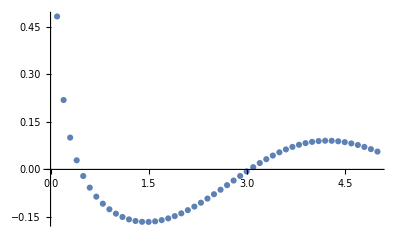

```mathematica
ListPlot[Re[Res]]
```

```mathematica
ListPlot[ParallelTable[{η,Re[CGrepeta[η,1.7,1]]},{η,-π,π,0.1}]]//RepeatedTiming
```

$Aborted

```mathematica
Distr2=N[GaussianQuadratureWeights[20,-π,π]];
Sum[CGrepeta[Distr2⟦i⟧⟦1⟧]*Distr2⟦i⟧⟦2⟧,{i,1,Length[Distr2]}]/(2π)//Timing
```

{0.479541,0.0717756-0.0569065 ⅈ}

```mathematica
δη=0.1;
G=Sum[CGrepeta[η]δη,{η,-π,π,δη}]/(2π)//Timing
```

$Aborted

#### Technical Tests

```mathematica
{f,cf}={Function[{p},√(θ[p]/π)Exp[ⅈ τ[p,1.7,1.]*0.5]],
Compile[{{p,_Real}},√(θ[p]/π)Exp[ⅈ τ[p,1.7,1.]*0.5]]};
Do[f[1.],{10^5}]//RepeatedTiming
Do[cf[1.],{10^5}]//RepeatedTiming
Plot[{f[x],cf[x]},{x,-π,π},PlotRange->{{Automatic,Automatic},{Automatic,Automatic}}]
```

{0.3575,Null}

{0.0702,Null}

-Graphics-

## Compiled. Test version. I inline functions by hand

names are formed as
compiled function ≡ cf

```mathematica
Needs["CCompilerDriver`"]
CCompilers[]
```

{{Name→GCC,Compiler→CCompilerDriver`GCCCompiler`GCCCompiler,CompilerInstallation→/usr/bin,CompilerName→Automatic}}

```mathematica
CEnergy=Compile[{{p,_Real}},
p*p*0.5
,Parallelization->True
,RuntimeAttributes->{Listable},
,CompilationTarget->CompilerName
];
```

Compile::nonopt: Options expected (instead of Null) beyond position 3 in Compile[{{p,_Real}},p p 0.5,Parallelization→True,RuntimeAttributes→{Listable},Null,CompilationTarget→CompilerName]. An option must be a rule or a list of rules.

```mathematica
(*
β=100.0;
μ=0.5*(π *0.5)^2;
x=1.7;
t=1.0;
*)
CompilerName="C";

CEminus=Compile[{{p,_Real},{x,_Real},{t,_Real}},
Block[{
energy=p*p*0.5,
τ=t*p*p*0.5-x*p,
μ= 0.5*(π *0.5)^2,
β0=100.0
 },
Sqrt[1./π 1.0/(Exp[β0*(energy-μ)]+1.0)]*Exp[ⅈ *τ*0.5]
]
,RuntimeOptions->"Speed"
,CompilationTarget->CompilerName
,CompilationOptions->{
"InlineCompiledFunctions"->True
,"InlineExternalDefinitions"->True
,"ExpressionOptimization"->True
}
];
(*Give better names*)
CEinfW=Compile[{{p,_Real},{η,_Real},{x,_Real},{t,_Real}},
Block[{
τ=t*p*p*0.5-x*p 
},
1./π*Sin[η*0.5]*(ⅈ π Exp[-ⅈ τ]*Erf[(x-p*t)*(1.-ⅈ)/(2*√t)])
+Cos[η*0.5]*Exp[-ⅈ *τ]
]
,RuntimeOptions->"Speed"
,CompilationTarget->CompilerName
,CompilationOptions->{
"InlineCompiledFunctions"->True
,"InlineExternalDefinitions"->True
,"ExpressionOptimization"->True
}
];



CV=Compile[{{p,_Real},{q,_Real},{η,_Real},{x,_Real},{t,_Real}},

Block[{ϵ=10^-6},Sin[η*0.5](CEinfW[p+ϵ,η,x,t]-CEinfW[q,η,x,t])/(p+ϵ-q)CEminus[q,x,t]*CEminus[p,x,t]]

,RuntimeOptions->"Speed"
,CompilationTarget->CompilerName
,CompilationOptions->{
"InlineCompiledFunctions"->True
,"InlineExternalDefinitions"->True
,"ExpressionOptimization"->True
}
];
CW=Compile[{{p,_Real},{q,_Real},{η,_Real},{x,_Real},{t,_Real}},
0.5*CEminus[p,x,t]*CEinfW[p,η,x,t]*CEminus[q,x,t]*CEinfW[q,η,x,t]
,RuntimeOptions->"Speed"
,CompilationTarget->CompilerName
,CompilationOptions->{
"InlineCompiledFunctions"->True
,"InlineExternalDefinitions"->True
,"ExpressionOptimization"->True
}
];
CMatrixElementV=Compile[{{i,_Integer},{j,_Integer},{p,_Real},{q,_Real},{ω1,_Real},{ω2,_Real},
{η,_Real},{x,_Real},{t,_Real}},
KroneckerDelta[i,j]+√ω1 CV[p,q,η,x,t] √ω2
,RuntimeOptions->"Speed"
,CompilationTarget->CompilerName
,CompilationOptions->{
"InlineCompiledFunctions"->True
,"InlineExternalDefinitions"->True
,"ExpressionOptimization"->True
}
];
CMatrixElementVW=Compile[{{i,_Integer},{j,_Integer},{p,_Real},{q,_Real},{ω1,_Real},{ω2,_Real},
{η,_Real},{x,_Real},{t,_Real}},
KroneckerDelta[i,j]+√ω1 (CV[p,q,η,x,t]-CW[p,q,η,x,t])√ω2
,CompilationTarget->CompilerName
,RuntimeOptions->"Speed"
,CompilationOptions->{
"InlineCompiledFunctions"->True
,"InlineExternalDefinitions"->True
,"ExpressionOptimization"->True
}
];

<<NumericalDifferentialEquationAnalysis`
Distr=N[GaussianQuadratureWeights[20,-π/2,π/2]];
MatrixV[η_,x_,t_]:=Table[CMatrixElementV[i,j,Distr⟦i⟧⟦1⟧,Distr⟦j⟧⟦1⟧,
Distr⟦i⟧⟦2⟧,Distr⟦j⟧⟦2⟧,η,x,t],
{i,1,Length[Distr]},{j,1,Length[Distr]}];


CDetMatrix1[η_,x_,t_]:=Det[Table[CMatrixElementV[i,j,Distr⟦i⟧⟦1⟧,Distr⟦j⟧⟦1⟧,
Distr⟦i⟧⟦2⟧,Distr⟦j⟧⟦2⟧,η,x,t],
{i,1,Length[Distr]},{j,1,Length[Distr]}]];
CDetMatrix2[η_,x_,t_]:=Det[Table[CMatrixElementVW[i,j,Distr⟦i⟧⟦1⟧,Distr⟦j⟧⟦1⟧,
Distr⟦i⟧⟦2⟧,Distr⟦j⟧⟦2⟧,η,x,t],
{i,1,Length[Distr]},{j,1,Length[Distr]}]];
CG0=Compile[{{x,_Real},{t,_Real}},Exp[(-ⅈ π)/4.] √(1/(2π t))Exp[ⅈ(x)^2/(2t)]];
CGrepeta[η_,x_,t_]:=(CG0[x,t]-1)CDetMatrix1[η,x,t]+CDetMatrix2[η,x,t];
Distr2=N[GaussianQuadratureWeights[20,-π,π]];
CGrep[x_,t_]:=1/(2π)ParallelSum[CGrepeta[Distr2⟦i⟧⟦1⟧ ,x,t]*Distr2⟦i⟧⟦2⟧,{i,1,Length[Distr2]}]
```

```mathematica
CGrepeta[η_,x_,t_]:=(CG0[x,t]-1)*
Det[
p[i_]:=Distr⟦i⟧⟦1⟧;
q[j_]:=Distr⟦j⟧⟦1⟧;
ω1[i_]:=Distr⟦i⟧⟦2⟧;
ω2[j_]:=Distr⟦j⟧⟦2⟧;
Table[
KroneckerDelta[i,j]+√ω1*
Block[{ϵ=10^-6},Sin[η*0.5](CEinfW[p+ϵ,η,x,t]-CEinfW[q,η,x,t])/(p+ϵ-q)CEminus[q,x,t]*CEminus[p,x,t]]
*√ω2
,{i,1,Length[Distr]},{j,1,Length[Distr]}
]
]

+Det[];
```

```mathematica
Function
```

```mathematica
CGrep[1.7,1.0]//AbsoluteTiming
f[η_?NumericQ]:=CGrepeta[η,1.7,1.0];
(*foo[Ef_?NumericQ]:=NIntegrate[f[x,Ef],{x,-EBoundary,EBoundary}],*)
1/(2π)NIntegrate[f[η],{η,-π,π},Method->{"GaussKronrodRule","Points"->10}]//AbsoluteTiming
```

{1.10849,0.0717448-0.0569097 ⅈ}

{2.2346,0.0717448-0.0569097 ⅈ}

```mathematica
Table[(k=0;
NIntegrate[x^10,{x,0,1},Method->{"GaussKronrodRule","Points"->i},EvaluationMonitor:>k++];k),{i,2,10}]
```

{284,91,63,33,13,15,17,19,21}

```mathematica
Needs["CCompilerDriver`"]
CCompilers[]
DefaultCCompiler[]
```

{{Name→GCC,Compiler→CCompilerDriver`GCCCompiler`GCCCompiler,CompilerInstallation→/usr/bin,CompilerName→Automatic}}

CCompilerDriver`GCCCompiler`GCCCompiler

```mathematica
(Res=Table[{t,CGrep[0,t]},{t,0.1,5,0.1}])//AbsoluteTiming
```

{36.9746,{{0.1,0.482574-0.886732 ⅈ},{0.2,0.218893-0.618536 ⅈ},{0.3,0.100433-0.49462 ⅈ},{0.4,0.0287418-0.41632 ⅈ},{0.5,-0.0207747-0.358883 ⅈ},{0.6,-0.0574962-0.312806 ⅈ},{0.7,-0.0858307-0.273597 ⅈ},{0.8,-0.108128-0.238851 ⅈ},{0.9,-0.125753-0.207184 ⅈ},{1.,-0.13955-0.177761 ⅈ},{1.1,-0.150066-0.150074 ⅈ},{1.2,-0.15768-0.123818 ⅈ},{1.3,-0.162663-0.0988188 ⅈ},{1.4,-0.165225-0.0749926 ⅈ},{1.5,-0.16554-0.0523173 ⅈ},{1.6,-0.16376-0.0308128 ⅈ},{1.7,-0.16003-0.0105276 ⅈ},{1.8,-0.154492+0.00847195 ⅈ},{1.9,-0.147294+0.0261092 ⅈ},{2.,-0.138585+0.042304 ⅈ},{2.1,-0.128527+0.0569779 ⅈ},{2.2,-0.117285+0.0700581 ⅈ},{2.3,-0.105034+0.0814817 ⅈ},{2.4,-0.0919546+0.0911976 ⅈ},{2.5,-0.0782321+0.0991695 ⅈ},{2.6,-0.0640555+0.105378 ⅈ},{2.7,-0.0496147+0.109819 ⅈ},{2.8,-0.0350987+0.11251 ⅈ},{2.9,-0.0206931+0.113485 ⅈ},{3.,-0.00657806+0.112797 ⅈ},{3.1,0.00707404+0.110516 ⅈ},{3.2,0.0201007+0.106731 ⅈ},{3.3,0.0323514+0.101545 ⅈ},{3.4,0.043689+0.0950769 ⅈ},{3.5,0.0539918+0.0874581 ⅈ},{3.6,0.0631545+0.0788308 ⅈ},{3.7,0.0710896+0.0693464 ⅈ},{3.8,0.0777278+0.059163 ⅈ},{3.9,0.0830188+0.0484435 ⅈ},{4.,0.0869314+0.0373533 ⅈ},{4.1,0.0894537+0.0260579 ⅈ},{4.2,0.0905924+0.0147209 ⅈ},{4.3,0.0903726+0.00350201 ⅈ},{4.4,0.0888371-0.00744512 ⅈ},{4.5,0.0860448-0.0179747 ⅈ},{4.6,0.0820702-0.0279505 ⅈ},{4.7,0.0770018-0.0372475 ⅈ},{4.8,0.0709403-0.0457529 ⅈ},{4.9,0.0639975-0.0533678 ⅈ},{5.,0.0562942-0.0600077 ⅈ}}}

```mathematica
(Res=Table[{t,CGrep[0,t]},{t,0.1,5,0.1}])//AbsoluteTiming
```

{34.7896,{{0.1,0.482574-0.886732 ⅈ},{0.2,0.218893-0.618536 ⅈ},{0.3,0.100433-0.49462 ⅈ},{0.4,0.0287418-0.41632 ⅈ},{0.5,-0.0207747-0.358883 ⅈ},{0.6,-0.0574962-0.312806 ⅈ},{0.7,-0.0858307-0.273597 ⅈ},{0.8,-0.108128-0.238851 ⅈ},{0.9,-0.125753-0.207184 ⅈ},{1.,-0.13955-0.177761 ⅈ},{1.1,-0.150066-0.150074 ⅈ},{1.2,-0.15768-0.123818 ⅈ},{1.3,-0.162663-0.0988188 ⅈ},{1.4,-0.165225-0.0749926 ⅈ},{1.5,-0.16554-0.0523173 ⅈ},{1.6,-0.16376-0.0308128 ⅈ},{1.7,-0.16003-0.0105276 ⅈ},{1.8,-0.154492+0.00847195 ⅈ},{1.9,-0.147294+0.0261092 ⅈ},{2.,-0.138585+0.042304 ⅈ},{2.1,-0.128527+0.0569779 ⅈ},{2.2,-0.117285+0.0700581 ⅈ},{2.3,-0.105034+0.0814817 ⅈ},{2.4,-0.0919546+0.0911976 ⅈ},{2.5,-0.0782321+0.0991695 ⅈ},{2.6,-0.0640555+0.105378 ⅈ},{2.7,-0.0496147+0.109819 ⅈ},{2.8,-0.0350987+0.11251 ⅈ},{2.9,-0.0206931+0.113485 ⅈ},{3.,-0.00657806+0.112797 ⅈ},{3.1,0.00707404+0.110516 ⅈ},{3.2,0.0201007+0.106731 ⅈ},{3.3,0.0323514+0.101545 ⅈ},{3.4,0.043689+0.0950769 ⅈ},{3.5,0.0539918+0.0874581 ⅈ},{3.6,0.0631545+0.0788308 ⅈ},{3.7,0.0710896+0.0693464 ⅈ},{3.8,0.0777278+0.059163 ⅈ},{3.9,0.0830188+0.0484435 ⅈ},{4.,0.0869314+0.0373533 ⅈ},{4.1,0.0894537+0.0260579 ⅈ},{4.2,0.0905924+0.0147209 ⅈ},{4.3,0.0903726+0.00350201 ⅈ},{4.4,0.0888371-0.00744512 ⅈ},{4.5,0.0860448-0.0179747 ⅈ},{4.6,0.0820702-0.0279505 ⅈ},{4.7,0.0770018-0.0372475 ⅈ},{4.8,0.0709403-0.0457529 ⅈ},{4.9,0.0639975-0.0533678 ⅈ},{5.,0.0562942-0.0600077 ⅈ}}}

```mathematica
CGrepeta[0.1,0.5,1.]//RepeatedTiming
```

{0.052,-0.0858206-0.088231 ⅈ}

```mathematica
CGrep[1.7,1.]//RepeatedTiming
```

{1.099,0.0717448-0.0569097 ⅈ}

```mathematica
Needs["CompiledFunctionTools`"]
```

```mathematica
CompilePrint[CV]
```

5 arguments
		4 Integer registers
		25 Real registers
		10 Complex registers
		Underflow checking off
		Overflow checking off
		Integer overflow checking off
		RuntimeAttributes -> {}

		R0 = A1
		R1 = A2
		R2 = A3
		R3 = A4
		R4 = A5
		R16 = 0.3183098861837907
		R24 = 1.
		I0 = 10
		R22 = 1.2337005501361697
		R23 = 100.
		C3 = 0. + 1. I
		I1 = 6
		C4 = 1. - 1. I
		R17 = 3.141592653589793
		C0 = 0. - 1. I
		I3 = 2
		R7 = 0.5
		R15 = 0.
		Result = C7

1	I2 = Power[ I0, I1]
2	R8 = I2
3	R5 = Reciprocal[ R8]
4	R8 = R2 * R7
5	R9 = Sin[ R8]
6	R8 = R0 + R5
7	R10 = R2
8	R11 = R3
9	R12 = R4
10	R18 = R12 * R8 * R8 * R7
11	R13 = R11 * R8
12	R14 = - R13
13	R18 = R18 + R14
14	R14 = R10 * R7
15	R19 = R14
16	C2 = R18 + R15 I
17	C8 = C0 * C2
18	C6 = C8
19	C8 = Exp[ C6]
20	C1 = C8
21	R14 = Sin[ R19]
22	R13 = R8 * R12
23	R20 = - R13
24	R13 = R11 + R20
25	R20 = Sqrt[ R12]
26	R21 = I3
27	R21 = R21 * R20
28	R20 = Reciprocal[ R21]
29	C8 = R20 + R15 I
30	C2 = C4 * C8
31	C8 = R13 + R15 I
32	C8 = C8 * C2
33	R13 = R8 * R12
34	R20 = - R13
35	R13 = R11 + R20
36	R20 = Sqrt[ R12]
37	R21 = I3
38	R21 = R21 * R20
39	R20 = Reciprocal[ R21]
40	C2 = R20 + R15 I
41	C9 = C4 * C2
42	C2 = R13 + R15 I
43	C2 = C2 * C9
44	C9 = MainEvaluate[ Hold[Erf][ C2]]
45	C8 = R17 + R15 I
46	C2 = C3 * C8 * C1 * C9
47	C9 = R16 + R15 I
48	C8 = R14 + R15 I
49	C9 = C9 * C8 * C2
50	R14 = Cos[ R19]
51	C2 = R14 + R15 I
52	C2 = C2 * C1
53	C9 = C9 + C2
54	R12 = R1
55	R11 = R2
56	R10 = R3
57	R8 = R4
58	R14 = R8 * R12 * R12 * R7
59	R19 = R10 * R12
60	R18 = - R19
61	R14 = R14 + R18
62	R18 = R11 * R7
63	R13 = R18
64	C6 = R14 + R15 I
65	C8 = C0 * C6
66	C2 = C8
67	C8 = Exp[ C2]
68	C1 = C8
69	R18 = Sin[ R13]
70	R19 = R12 * R8
71	R20 = - R19
72	R19 = R10 + R20
73	R20 = Sqrt[ R8]
74	R21 = I3
75	R21 = R21 * R20
76	R20 = Reciprocal[ R21]
77	C8 = R20 + R15 I
78	C6 = C4 * C8
79	C8 = R19 + R15 I
80	C8 = C8 * C6
81	R19 = R12 * R8
82	R20 = - R19
83	R19 = R10 + R20
84	R20 = Sqrt[ R8]
85	R21 = I3
86	R21 = R21 * R20
87	R20 = Reciprocal[ R21]
88	C6 = R20 + R15 I
89	C5 = C4 * C6
90	C6 = R19 + R15 I
91	C6 = C6 * C5
92	C5 = MainEvaluate[ Hold[Erf][ C6]]
93	C8 = R17 + R15 I
94	C6 = C3 * C8 * C1 * C5
95	C5 = R16 + R15 I
96	C8 = R18 + R15 I
97	C5 = C5 * C8 * C6
98	R18 = Cos[ R13]
99	C6 = R18 + R15 I
100	C6 = C6 * C1
101	C5 = C5 + C6
102	C7 = - C5
103	C9 = C9 + C7
104	R8 = - R1
105	R10 = R0 + R5 + R8
106	R8 = Reciprocal[ R10]
107	C7 = R8 + R15 I
108	C9 = C9 * C7
109	R8 = R1
110	R10 = R3
111	R11 = R4
112	R12 = R11 * R8 * R8 * R7
113	R13 = R10 * R8
114	R14 = - R13
115	R12 = R12 + R14
116	R14 = R8 * R8 * R7
117	R19 = Reciprocal[ R17]
118	R21 = - R22
119	R13 = R14 + R21
120	R21 = R23 * R13
121	R13 = Exp[ R21]
122	R13 = R13 + R24
123	R21 = Reciprocal[ R13]
124	R13 = R24 * R21
125	R19 = R19 * R13
126	R13 = Sqrt[ R19]
127	C7 = R12 + R15 I
128	C5 = R7 + R15 I
129	C1 = C3 * C7 * C5
130	C7 = Exp[ C1]
131	C1 = R13 + R15 I
132	C1 = C1 * C7
133	R11 = R0
134	R10 = R3
135	R8 = R4
136	R14 = R8 * R11 * R11 * R7
137	R12 = R10 * R11
138	R13 = - R12
139	R14 = R14 + R13
140	R13 = R11 * R11 * R7
141	R12 = Reciprocal[ R17]
142	R19 = - R22
143	R21 = R13 + R19
144	R19 = R23 * R21
145	R21 = Exp[ R19]
146	R21 = R21 + R24
147	R19 = Reciprocal[ R21]
148	R21 = R24 * R19
149	R12 = R12 * R21
150	R21 = Sqrt[ R12]
151	C7 = R14 + R15 I
152	C5 = R7 + R15 I
153	C2 = C3 * C7 * C5
154	C7 = Exp[ C2]
155	C2 = R21 + R15 I
156	C2 = C2 * C7
157	C7 = R9 + R15 I
158	C7 = C7 * C9 * C1 * C2
159	Return

#### Technical Tests

```mathematica
{f,cf}={Function[{p},√(θ[p]/π)Exp[ⅈ τ[p,1.7,1.]*0.5]],
Compile[{{p,_Real}},√(θ[p]/π)Exp[ⅈ τ[p,1.7,1.]*0.5]]};
Do[f[1.],{10^5}]//RepeatedTiming
Do[cf[1.],{10^5}]//RepeatedTiming
Plot[{f[x],cf[x]},{x,-π,π},PlotRange->{{Automatic,Automatic},{Automatic,Automatic}}]
```

{0.3575,Null}

{0.0702,Null}

-Graphics-

## Compiled. Test version2

names are formed as
compiled function ≡ cf

```mathematica
Needs["CCompilerDriver`"]
CCompilers[]
```

{{Name→GCC,Compiler→CCompilerDriver`GCCCompiler`GCCCompiler,CompilerInstallation→/usr/bin,CompilerName→Automatic}}

```mathematica
CompilerName="C";

CV=Compile[{{p,_Real},{q,_Real},{η,_Real},{x,_Real},{t,_Real}},
Block[{ϵ=10^-6,
energyp=p*p*0.5,
τp=t*p*p*0.5-x*p,
τpϵ=t*(p+ϵ)*(p+ϵ)*0.5-x*(p+ϵ),

energyq=q*q*0.5,
τq=t*q*q*0.5-x*q,

μ= 0.5*(π *0.5)^2,
β0=100.0
},
Sin[η*0.5]*
(
( Exp[-ⅈ τpϵ](1./π*Sin[η*0.5]*(ⅈ π Erf[(x-(p+ϵ)*t)*(1.-ⅈ)/(2*√t)])
+Cos[η*0.5])-
Exp[-ⅈ τq]*(1./π*Sin[η*0.5]*(ⅈ π Erf[(x-q*t)*(1.-ⅈ)/(2*√t)])
+Cos[η*0.5]))/(p+ϵ-q)
)*
Sqrt[1./π 1.0/(Exp[β0*(energyq-μ)]+1.0)]*Exp[ⅈ *τq*0.5]*
Sqrt[1./π 1.0/(Exp[β0*(energyp-μ)]+1.0)]*Exp[ⅈ *τp*0.5]
]
,Parallelization->True
,RuntimeOptions->"Speed"
,CompilationTarget->CompilerName
,CompilationOptions->{
"InlineCompiledFunctions"->True
,"InlineExternalDefinitions"->True
,"ExpressionOptimization"->True
}
];
CW=Compile[{{p,_Real},{q,_Real},{η,_Real},{x,_Real},{t,_Real}},
Block[{
energyp=p*p*0.5,
τp=t*p*p*0.5-x*p,

energyq=q*q*0.5,
τq=t*q*q*0.5-x*q,

μ= 0.5*(π *0.5)^2,
β0=100.0
},
0.5*
Sqrt[1./π 1.0/(Exp[β0*(energyp-μ)]+1.0)]*Exp[ⅈ *τp*0.5]*
Sqrt[1./π 1.0/(Exp[β0*(energyq-μ)]+1.0)]*Exp[ⅈ *τq*0.5]*
Exp[-ⅈ τp]*(1./π*Sin[η*0.5](ⅈ π Erf[(x-p*t)*(1.-ⅈ)/(2*√t)])
+Cos[η*0.5])*
 Exp[-ⅈ τq]*(1./π*Sin[η*0.5](ⅈ π Erf[(x-q*t)*(1.-ⅈ)/(2*√t)])
+Cos[η*0.5])
]
,Parallelization->True
,RuntimeOptions->"Speed"
,CompilationTarget->CompilerName
,CompilationOptions->{
"InlineCompiledFunctions"->True
,"InlineExternalDefinitions"->True
,"ExpressionOptimization"->True
}
];
CMatrixElementV=Compile[{{i,_Real},{j,_Real},{p,_Real},{q,_Real},{ω1,_Real},{ω2,_Real},
{η,_Real},{x,_Real},{t,_Real}},
KroneckerDelta[i,j]+√ω1 CV[p,q,η,x,t] √ω2
,Parallelization->True
,RuntimeOptions->"Speed"
,CompilationTarget->CompilerName
,CompilationOptions->{
"InlineCompiledFunctions"->True
,"InlineExternalDefinitions"->True
,"ExpressionOptimization"->True
}
];
CMatrixElementVW=Compile[{{i,_Real},{j,_Real},{p,_Real},{q,_Real},{ω1,_Real},{ω2,_Real},
{η,_Real},{x,_Real},{t,_Real}},
KroneckerDelta[i,j]+√ω1 (CV[p,q,η,x,t]-CW[p,q,η,x,t])√ω2
,Parallelization->True
,CompilationTarget->CompilerName
,RuntimeOptions->"Speed"
,CompilationOptions->{
"InlineCompiledFunctions"->True
,"InlineExternalDefinitions"->True
,"ExpressionOptimization"->True
}
];

<<NumericalDifferentialEquationAnalysis`
Distr=N[GaussianQuadratureWeights[20,-π/2,π/2]];

CDetMatrix1[η_,x_,t_]:=Det[Table[CMatrixElementV[i,j,Distr⟦i⟧⟦1⟧,Distr⟦j⟧⟦1⟧,
Distr⟦i⟧⟦2⟧,Distr⟦j⟧⟦2⟧,η,x,t],
{i,1,Length[Distr]},{j,1,Length[Distr]}]];
CDetMatrix2[η_,x_,t_]:=Det[Table[CMatrixElementVW[i,j,Distr⟦i⟧⟦1⟧,Distr⟦j⟧⟦1⟧,
Distr⟦i⟧⟦2⟧,Distr⟦j⟧⟦2⟧,η,x,t],
{i,1,Length[Distr]},{j,1,Length[Distr]}]];
CG0=Compile[{{x,_Real},{t,_Real}},Exp[(-ⅈ π)/4.] √(1./(2.π t))Exp[ⅈ(x*x)/(2.t)]];
CGrepeta[η_,x_,t_]:=(CG0[x,t]-1)CDetMatrix1[η,x,t]+CDetMatrix2[η,x,t];
Distr2=N[GaussianQuadratureWeights[20,-π,π]];
CGrep[x_,t_]:=1/(2π)ParallelSum[CGrepeta[Distr2⟦i⟧⟦1⟧ ,x,t]*Distr2⟦i⟧⟦2⟧,{i,1,Length[Distr2]}]
```

```mathematica
CDetMatrix1[1,1.7,1]//AbsoluteTiming
```

{0.039534,0.599168+0.627103 ⅈ}

```mathematica
Developer`ToPackedArray[Table[CMatrixElementV[i,j,Distr⟦i⟧⟦1⟧,Distr⟦j⟧⟦1⟧,
Distr⟦i⟧⟦2⟧,Distr⟦j⟧⟦2⟧,1.,1.7,1.],
{i,1,Length[Distr]},{j,1,Length[Distr]}]]//Det//AbsoluteTiming
```

{0.041609,0.599168+0.627103 ⅈ}

```mathematica
Det[Table[1./(1+Abs[i-j]),
{i,1,Length[Distr]},{j,1,Length[Distr]}]]//AbsoluteTiming
```

{0.000981,0.00294022}

```mathematica
CGrep[1.7,1.0]//AbsoluteTiming
f[η_?NumericQ]:=CGrepeta[η,1.7,1.0];
(*foo[Ef_?NumericQ]:=NIntegrate[f[x,Ef],{x,-EBoundary,EBoundary}],*)
1/(2π)NIntegrate[f[η],{η,-π,π},Method->{"GaussKronrodRule","Points"->10}]//AbsoluteTiming
```

{1.17804,0.0717448-0.0569097 ⅈ}

{2.21205,0.0717448-0.0569097 ⅈ}

{1.12732,0.0717448-0.0569097 ⅈ}

{2.19713,0.0717448-0.0569097 ⅈ}

```mathematica
Needs["CCompilerDriver`"]
CCompilers[]
DefaultCCompiler[]
```

{{Name→GCC,Compiler→CCompilerDriver`GCCCompiler`GCCCompiler,CompilerInstallation→/usr/bin,CompilerName→Automatic}}

CCompilerDriver`GCCCompiler`GCCCompiler

```mathematica
(Res=Table[{t,CGrep[0,t]},{t,0.1,5,0.1}])//AbsoluteTiming
```

{40.5834,{{0.1,0.482574-0.886732 ⅈ},{0.2,0.218893-0.618536 ⅈ},{0.3,0.100433-0.49462 ⅈ},{0.4,0.0287418-0.41632 ⅈ},{0.5,-0.0207747-0.358883 ⅈ},{0.6,-0.0574962-0.312806 ⅈ},{0.7,-0.0858307-0.273597 ⅈ},{0.8,-0.108128-0.238851 ⅈ},{0.9,-0.125753-0.207184 ⅈ},{1.,-0.13955-0.177761 ⅈ},{1.1,-0.150066-0.150074 ⅈ},{1.2,-0.15768-0.123818 ⅈ},{1.3,-0.162663-0.0988188 ⅈ},{1.4,-0.165225-0.0749926 ⅈ},{1.5,-0.16554-0.0523173 ⅈ},{1.6,-0.16376-0.0308128 ⅈ},{1.7,-0.16003-0.0105276 ⅈ},{1.8,-0.154492+0.00847195 ⅈ},{1.9,-0.147294+0.0261092 ⅈ},{2.,-0.138585+0.042304 ⅈ},{2.1,-0.128527+0.0569779 ⅈ},{2.2,-0.117285+0.0700581 ⅈ},{2.3,-0.105034+0.0814817 ⅈ},{2.4,-0.0919546+0.0911976 ⅈ},{2.5,-0.0782321+0.0991695 ⅈ},{2.6,-0.0640555+0.105378 ⅈ},{2.7,-0.0496147+0.109819 ⅈ},{2.8,-0.0350987+0.11251 ⅈ},{2.9,-0.0206931+0.113485 ⅈ},{3.,-0.00657806+0.112797 ⅈ},{3.1,0.00707404+0.110516 ⅈ},{3.2,0.0201007+0.106731 ⅈ},{3.3,0.0323514+0.101545 ⅈ},{3.4,0.043689+0.0950769 ⅈ},{3.5,0.0539918+0.0874581 ⅈ},{3.6,0.0631545+0.0788308 ⅈ},{3.7,0.0710896+0.0693464 ⅈ},{3.8,0.0777278+0.059163 ⅈ},{3.9,0.0830188+0.0484435 ⅈ},{4.,0.0869314+0.0373533 ⅈ},{4.1,0.0894537+0.0260579 ⅈ},{4.2,0.0905924+0.0147209 ⅈ},{4.3,0.0903726+0.00350201 ⅈ},{4.4,0.0888371-0.00744512 ⅈ},{4.5,0.0860448-0.0179747 ⅈ},{4.6,0.0820702-0.0279505 ⅈ},{4.7,0.0770018-0.0372475 ⅈ},{4.8,0.0709403-0.0457529 ⅈ},{4.9,0.0639975-0.0533678 ⅈ},{5.,0.0562942-0.0600077 ⅈ}}}

```mathematica
(Res=Table[{t,CGrep[0,t]},{t,0.1,5,0.1}])//AbsoluteTiming
```

{34.7896,{{0.1,0.482574-0.886732 ⅈ},{0.2,0.218893-0.618536 ⅈ},{0.3,0.100433-0.49462 ⅈ},{0.4,0.0287418-0.41632 ⅈ},{0.5,-0.0207747-0.358883 ⅈ},{0.6,-0.0574962-0.312806 ⅈ},{0.7,-0.0858307-0.273597 ⅈ},{0.8,-0.108128-0.238851 ⅈ},{0.9,-0.125753-0.207184 ⅈ},{1.,-0.13955-0.177761 ⅈ},{1.1,-0.150066-0.150074 ⅈ},{1.2,-0.15768-0.123818 ⅈ},{1.3,-0.162663-0.0988188 ⅈ},{1.4,-0.165225-0.0749926 ⅈ},{1.5,-0.16554-0.0523173 ⅈ},{1.6,-0.16376-0.0308128 ⅈ},{1.7,-0.16003-0.0105276 ⅈ},{1.8,-0.154492+0.00847195 ⅈ},{1.9,-0.147294+0.0261092 ⅈ},{2.,-0.138585+0.042304 ⅈ},{2.1,-0.128527+0.0569779 ⅈ},{2.2,-0.117285+0.0700581 ⅈ},{2.3,-0.105034+0.0814817 ⅈ},{2.4,-0.0919546+0.0911976 ⅈ},{2.5,-0.0782321+0.0991695 ⅈ},{2.6,-0.0640555+0.105378 ⅈ},{2.7,-0.0496147+0.109819 ⅈ},{2.8,-0.0350987+0.11251 ⅈ},{2.9,-0.0206931+0.113485 ⅈ},{3.,-0.00657806+0.112797 ⅈ},{3.1,0.00707404+0.110516 ⅈ},{3.2,0.0201007+0.106731 ⅈ},{3.3,0.0323514+0.101545 ⅈ},{3.4,0.043689+0.0950769 ⅈ},{3.5,0.0539918+0.0874581 ⅈ},{3.6,0.0631545+0.0788308 ⅈ},{3.7,0.0710896+0.0693464 ⅈ},{3.8,0.0777278+0.059163 ⅈ},{3.9,0.0830188+0.0484435 ⅈ},{4.,0.0869314+0.0373533 ⅈ},{4.1,0.0894537+0.0260579 ⅈ},{4.2,0.0905924+0.0147209 ⅈ},{4.3,0.0903726+0.00350201 ⅈ},{4.4,0.0888371-0.00744512 ⅈ},{4.5,0.0860448-0.0179747 ⅈ},{4.6,0.0820702-0.0279505 ⅈ},{4.7,0.0770018-0.0372475 ⅈ},{4.8,0.0709403-0.0457529 ⅈ},{4.9,0.0639975-0.0533678 ⅈ},{5.,0.0562942-0.0600077 ⅈ}}}

```mathematica
CGrepeta[0.1,0.5,1.]//RepeatedTiming
```

{0.052,-0.0858206-0.088231 ⅈ}

```mathematica
CGrep[1.7,1.]//RepeatedTiming
```

{1.099,0.0717448-0.0569097 ⅈ}

```mathematica
Needs["CompiledFunctionTools`"]
```

```mathematica
CompilePrint[CV]
```

5 arguments
		4 Integer registers
		31 Real registers
		10 Complex registers
		Underflow checking off
		Overflow checking off
		Integer overflow checking off
		RuntimeAttributes -> {}

		R0 = A1
		R1 = A2
		R2 = A3
		R3 = A4
		R4 = A5
		R22 = 0.3183098861837907
		R29 = 1.
		I0 = 10
		R14 = 1.2337005501361697
		R15 = 100.
		C5 = 0. + 1. I
		I1 = 6
		C0 = 1. - 1. I
		R23 = 3.141592653589793
		I3 = 2
		C3 = 0. - 1. I
		R7 = 0.5
		R19 = 0.
		Result = C6

1	I2 = Power[ I0, I1]
2	R16 = I2
3	R12 = Reciprocal[ R16]
4	R16 = R0 * R0 * R7
5	R13 = R4 * R0 * R0 * R7
6	R17 = R3 * R0
7	R20 = - R17
8	R13 = R13 + R20
9	R20 = R0 + R12
10	R17 = R0 + R12
11	R18 = R4 * R20 * R17 * R7
12	R20 = R0 + R12
13	R17 = R3 * R20
14	R20 = - R17
15	R18 = R18 + R20
16	R20 = R1 * R1 * R7
17	R17 = R4 * R1 * R1 * R7
18	R10 = R3 * R1
19	R26 = - R10
20	R17 = R17 + R26
21	R26 = R14
22	R10 = R15
23	R27 = R2 * R7
24	R25 = R27
25	R27 = Sin[ R25]
26	R24 = R27
27	R27 = Sqrt[ R4]
28	R8 = R27
29	R27 = I3
30	R27 = R27 * R8
31	R5 = R27
32	R27 = Reciprocal[ R5]
33	R6 = R27
34	C2 = R6 + R19 I
35	C1 = C0 * C2
36	C4 = C1
37	R27 = Cos[ R25]
38	R11 = R27
39	R27 = - R26
40	R9 = R27
41	C1 = R18 + R19 I
42	C2 = C3 * C1
43	C1 = Exp[ C2]
44	R27 = R0 + R12
45	R27 = R27 * R4
46	R28 = - R27
47	R27 = R3 + R28
48	C2 = R27 + R19 I
49	C2 = C2 * C4
50	R27 = R0 + R12
51	R27 = R27 * R4
52	R28 = - R27
53	R27 = R3 + R28
54	C6 = R27 + R19 I
55	C6 = C6 * C4
56	C7 = MainEvaluate[ Hold[Erf][ C6]]
57	C2 = R23 + R19 I
58	C6 = C5 * C2 * C7
59	C7 = R22 + R19 I
60	C2 = R24 + R19 I
61	C7 = C7 * C2 * C6
62	C6 = R11 + R19 I
63	C7 = C7 + C6
64	C1 = C1 * C7
65	C7 = R17 + R19 I
66	C6 = C3 * C7
67	C7 = Exp[ C6]
68	R27 = R1 * R4
69	R28 = - R27
70	R27 = R3 + R28
71	C6 = R27 + R19 I
72	C6 = C6 * C4
73	R27 = R1 * R4
74	R28 = - R27
75	R27 = R3 + R28
76	C2 = R27 + R19 I
77	C2 = C2 * C4
78	C8 = MainEvaluate[ Hold[Erf][ C2]]
79	C6 = R23 + R19 I
80	C2 = C5 * C6 * C8
81	C8 = R22 + R19 I
82	C6 = R24 + R19 I
83	C8 = C8 * C6 * C2
84	C2 = R11 + R19 I
85	C8 = C8 + C2
86	C7 = C7 * C8
87	C8 = - C7
88	C1 = C1 + C8
89	R27 = - R1
90	R28 = R0 + R12 + R27
91	R27 = Reciprocal[ R28]
92	C8 = R27 + R19 I
93	C1 = C1 * C8
94	R28 = R20 + R9
95	R27 = R10 * R28
96	R28 = Exp[ R27]
97	R28 = R28 + R29
98	R27 = Reciprocal[ R28]
99	R28 = R29 * R27
100	R27 = R22 * R28
101	R28 = Sqrt[ R27]
102	C8 = R17 + R19 I
103	C7 = R7 + R19 I
104	C2 = C5 * C8 * C7
105	C8 = Exp[ C2]
106	R27 = R16 + R9
107	R30 = R10 * R27
108	R27 = Exp[ R30]
109	R27 = R27 + R29
110	R30 = Reciprocal[ R27]
111	R27 = R29 * R30
112	R30 = R22 * R27
113	R27 = Sqrt[ R30]
114	C2 = R13 + R19 I
115	C7 = R7 + R19 I
116	C6 = C5 * C2 * C7
117	C2 = Exp[ C6]
118	C6 = R24 + R19 I
119	C7 = R28 + R19 I
120	C9 = R27 + R19 I
121	C6 = C6 * C1 * C7 * C8 * C9 * C2
122	Return

#### Technical Tests

```mathematica
{f,cf}={Function[{p},√(θ[p]/π)Exp[ⅈ τ[p,1.7,1.]*0.5]],
Compile[{{p,_Real}},√(θ[p]/π)Exp[ⅈ τ[p,1.7,1.]*0.5]]};
Do[f[1.],{10^5}]//RepeatedTiming
Do[cf[1.],{10^5}]//RepeatedTiming
Plot[{f[x],cf[x]},{x,-π,π},PlotRange->{{Automatic,Automatic},{Automatic,Automatic}}]
```

{0.3575,Null}

{0.0702,Null}

-Graphics-

## Compiled. Linearization of the matrix elem

```mathematica
Grep[x_,t_]:=ParallelSum[Grepeta[Distr2⟦i⟧⟦1⟧ ,x,t]*Distr2⟦i⟧⟦2⟧,{i,1,Length[Distr2]}]/(2π)
```

```mathematica
Grepeta[0.1,0.5,1.]//RepeatedTiming
```

{0.0951,-0.0858206-0.088231 ⅈ}

```mathematica
Clear[f]
```

```mathematica
<<NumericalDifferentialEquationAnalysis`
Distr=N[GaussianQuadratureWeights[4,-π/2,π/2]];
f=Function[{η,x,t,G}, Block[{
(*G=DisrtibGauss,*)
ϵ=10^-6,

τ=Table[t*(G⟦i,1⟧)^2*0.5-x*G⟦i,1⟧,{i,1,Length[G]}],
τϵ=Table[t*(G⟦i,1⟧+ϵ)^2*0.5-x*(G⟦i,1⟧+ϵ),{i,1,Length[G]}],
θ=Table[1.0/(Exp[100.0*((G⟦i,1⟧)^2*0.5-(0.5*(π *0.5)^2))]+1.0),{i,1,Length[G]}],
Emin=Table[Sqrt[θ⟦i⟧/π]*Exp[ⅈ τ⟦i⟧*0.5],{i,1,Length[G]}],(*η НЕ входит! не нужно считать занова*)
EinftyW=Table[Exp[-ⅈ τ⟦i⟧](Sin[η*0.5]ⅈ Erf[(x-G⟦i,1⟧*t)(1.-ⅈ)/(2 √t)]+Cos[η*0.5]),{i,1,Length[G]}],
EinftyWϵ=Table[Exp[-ⅈ τϵ⟦i⟧](Sin[η*0.5]ⅈ Erf[(x-(G⟦i,1⟧+ϵ)*t)(1.-ⅈ)/(2 √t)]+Cos[η*0.5]),{i,1,Length[G]}],

(*Einfty=Table[Sin[η*0.5]EinftyW⟦i⟧,{i,1,Length[Distr]}](*η только в sin и cos ! не нужно считать занова*),
Einftyϵ=Table[Sin[η*0.5]EinftyWϵ⟦i⟧,{i,1,Length[Distr]}],
*)
(*V=Table[(Einftyϵ⟦i⟧-Einfty⟦j⟧)/(Distr⟦i⟧⟦1⟧+ϵ-Distr⟦j⟧⟦1⟧)Emin⟦i⟧*Emin⟦j⟧,{i,1,Length[Distr]},{j,1,Length[Distr]}],
WV=Table[V⟦i,j⟧-0.5*Emin⟦i⟧*Emin⟦j⟧*EinftyW⟦i⟧*EinftyW⟦j⟧,{i,1,Length[Distr]},{j,1,Length[Distr]}],*)
detV=Det[Table[KroneckerDelta[i,j]+√G⟦i,2⟧ (Emin⟦i⟧*Emin⟦j⟧*Sin[η*0.5](EinftyWϵ⟦i⟧-EinftyW⟦j⟧)/(G⟦i,1⟧+ϵ-G⟦j,1⟧))√G⟦j,2⟧,{i,1,Length[G]},{j,1,Length[G]}]],
detWV=Det[Table[KroneckerDelta[i,j]+√G⟦i,2⟧ (
Emin⟦i⟧*Emin⟦j⟧(Sin[η*0.5](EinftyWϵ⟦i⟧-EinftyW⟦j⟧)/(G⟦i,1⟧+ϵ-G⟦j,1⟧)-0.5*EinftyW⟦i⟧*EinftyW⟦j⟧)
)√G⟦j,2⟧,{i,1,Length[G]},{j,1,Length[G]}]]
},
(Exp[(-ⅈ π)/4.] √(1./(2.π t))Exp[ⅈ(x*x)/(2.t)]-1)detV+detWV
]];
```

```mathematica
Distr=N[GaussianQuadratureWeights[20,-π/2,π/2]];
CGrepeta=Compile[{{η,_Real},{x,_Real},{t,_Real}},
Block[{G=Distr},
f[η,x,t,G]
]
,RuntimeOptions->"Speed"
,CompilationTarget->"C"
,CompilationOptions->{
"InlineCompiledFunctions"->True
,"InlineExternalDefinitions"->True
,"ExpressionOptimization"->True
}
];
(*f[0.1,0.5,1.,Distr]//AbsoluteTiming
CGrepeta[0.1,0.5,1.]//RepeatedTiming*)
Distr2=N[GaussianQuadratureWeights[20,-π,π]];
CGrep[x_,t_]:=1/(2π)ParallelSum[CGrepeta[Distr2⟦i,1⟧ ,x,t]*Distr2⟦i,2⟧,{i,1,Length[Distr2]}]
```

```mathematica
Needs["CompiledFunctionTools`"]
CompilePrint[Cf]
```

```mathematica
Grepeta[0.1,0.5,1.]//RepeatedTiming
```

{0.0951,-0.0858206-0.088231 ⅈ}

```mathematica
(Res0=Table[{t,CGrep[0,t]},{t,0.1,5,0.1}])//AbsoluteTiming
```

{1.81964,{{0.1,0.482574-0.886732 ⅈ},{0.2,0.218893-0.618536 ⅈ},{0.3,0.100433-0.49462 ⅈ},{0.4,0.0287418-0.41632 ⅈ},{0.5,-0.0207747-0.358883 ⅈ},{0.6,-0.0574962-0.312806 ⅈ},{0.7,-0.0858307-0.273597 ⅈ},{0.8,-0.108128-0.238851 ⅈ},{0.9,-0.125753-0.207184 ⅈ},{1.,-0.13955-0.177761 ⅈ},{1.1,-0.150066-0.150074 ⅈ},{1.2,-0.15768-0.123818 ⅈ},{1.3,-0.162663-0.0988188 ⅈ},{1.4,-0.165225-0.0749926 ⅈ},{1.5,-0.16554-0.0523173 ⅈ},{1.6,-0.16376-0.0308128 ⅈ},{1.7,-0.16003-0.0105276 ⅈ},{1.8,-0.154492+0.00847195 ⅈ},{1.9,-0.147294+0.0261092 ⅈ},{2.,-0.138585+0.042304 ⅈ},{2.1,-0.128527+0.0569779 ⅈ},{2.2,-0.117285+0.0700581 ⅈ},{2.3,-0.105034+0.0814817 ⅈ},{2.4,-0.0919546+0.0911976 ⅈ},{2.5,-0.0782321+0.0991695 ⅈ},{2.6,-0.0640555+0.105378 ⅈ},{2.7,-0.0496147+0.109819 ⅈ},{2.8,-0.0350987+0.11251 ⅈ},{2.9,-0.0206931+0.113485 ⅈ},{3.,-0.00657806+0.112797 ⅈ},{3.1,0.00707404+0.110516 ⅈ},{3.2,0.0201007+0.106731 ⅈ},{3.3,0.0323514+0.101545 ⅈ},{3.4,0.043689+0.0950769 ⅈ},{3.5,0.0539918+0.0874581 ⅈ},{3.6,0.0631545+0.0788308 ⅈ},{3.7,0.0710896+0.0693464 ⅈ},{3.8,0.0777278+0.059163 ⅈ},{3.9,0.0830188+0.0484435 ⅈ},{4.,0.0869314+0.0373533 ⅈ},{4.1,0.0894537+0.0260579 ⅈ},{4.2,0.0905924+0.0147209 ⅈ},{4.3,0.0903726+0.00350201 ⅈ},{4.4,0.0888371-0.00744512 ⅈ},{4.5,0.0860448-0.0179747 ⅈ},{4.6,0.0820702-0.0279505 ⅈ},{4.7,0.0770018-0.0372475 ⅈ},{4.8,0.0709403-0.0457529 ⅈ},{4.9,0.0639975-0.0533678 ⅈ},{5.,0.0562942-0.0600077 ⅈ}}}

```mathematica
(Res0=Table[{t,Grep[0,t]},{t,0.1,5,0.1}])//AbsoluteTiming
```

{77.7826,{{0.1,0.482574-0.886732 ⅈ},{0.2,0.218893-0.618536 ⅈ},{0.3,0.100433-0.49462 ⅈ},{0.4,0.0287418-0.41632 ⅈ},{0.5,-0.0207747-0.358883 ⅈ},{0.6,-0.0574962-0.312806 ⅈ},{0.7,-0.0858307-0.273597 ⅈ},{0.8,-0.108128-0.238851 ⅈ},{0.9,-0.125753-0.207184 ⅈ},{1.,-0.13955-0.177761 ⅈ},{1.1,-0.150066-0.150074 ⅈ},{1.2,-0.15768-0.123818 ⅈ},{1.3,-0.162663-0.0988188 ⅈ},{1.4,-0.165225-0.0749926 ⅈ},{1.5,-0.16554-0.0523173 ⅈ},{1.6,-0.16376-0.0308128 ⅈ},{1.7,-0.16003-0.0105276 ⅈ},{1.8,-0.154492+0.00847195 ⅈ},{1.9,-0.147294+0.0261092 ⅈ},{2.,-0.138585+0.042304 ⅈ},{2.1,-0.128527+0.0569779 ⅈ},{2.2,-0.117285+0.0700581 ⅈ},{2.3,-0.105034+0.0814817 ⅈ},{2.4,-0.0919546+0.0911976 ⅈ},{2.5,-0.0782321+0.0991695 ⅈ},{2.6,-0.0640555+0.105378 ⅈ},{2.7,-0.0496147+0.109819 ⅈ},{2.8,-0.0350987+0.11251 ⅈ},{2.9,-0.0206931+0.113485 ⅈ},{3.,-0.00657806+0.112797 ⅈ},{3.1,0.00707404+0.110516 ⅈ},{3.2,0.0201007+0.106731 ⅈ},{3.3,0.0323514+0.101545 ⅈ},{3.4,0.043689+0.0950769 ⅈ},{3.5,0.0539918+0.0874581 ⅈ},{3.6,0.0631545+0.0788308 ⅈ},{3.7,0.0710896+0.0693464 ⅈ},{3.8,0.0777278+0.059163 ⅈ},{3.9,0.0830188+0.0484435 ⅈ},{4.,0.0869314+0.0373533 ⅈ},{4.1,0.0894537+0.0260579 ⅈ},{4.2,0.0905924+0.0147209 ⅈ},{4.3,0.0903726+0.00350201 ⅈ},{4.4,0.0888371-0.00744512 ⅈ},{4.5,0.0860448-0.0179747 ⅈ},{4.6,0.0820702-0.0279505 ⅈ},{4.7,0.0770018-0.0372475 ⅈ},{4.8,0.0709403-0.0457529 ⅈ},{4.9,0.0639975-0.0533678 ⅈ},{5.,0.0562942-0.0600077 ⅈ}}}

## Not Compiled

```mathematica
β=100.0;
μ=0.5*(π *0.5)^2;

(*
x=1.7;
t=1.0;
*)

(*CEnergy=Compile[{{p,_Real}},p*p*0.5];*)
τ[p_,x_,t_]=t*p*p*0.5-x*p;
PV[p_,x_,t_]=ⅈ π Exp[-ⅈ τ[p,x,t]]*Erf[(x-p*t)(1.-ⅈ)/(2 √t)];
θ[p_]=1.0/(Exp[β*(p*p*0.5-μ)]+1.0);
Eminus[p_,x_,t_]=Sqrt[θ[p]/π]*Exp[ⅈ τ[p,x,t]*0.5];
Einf[p_,η_,x_,t_]=Sin[η*0.5]*Sin[η*0.5] 1./π PV[p,x,t]+Sin[η*0.5]Cos[η*0.5]Exp[-ⅈ τ[p,x,t]];
EinfW[p_,η_,x_,t_]=Sin[η*0.5] 1./π PV[p,x,t]+Cos[η*0.5]Exp[-ⅈ τ[p,x,t]];
Eplus[p_,η_,x_,t_]=Eminus[p,x,t]*Einf[p,η,x,t];
ϵ=10^-6;
V[p_,q_,η_,x_,t_]=(Eplus[p+ϵ,η,x,t]*Eminus[q,x,t]-Eplus[q,η,x,t]*Eminus[p+ϵ,x,t])/(p+ϵ-q);
W[p_,q_,η_,x_,t_]=
0.5*Eminus[p,x,t]*EinfW[p,η,x,t]*Eminus[q,x,t]*EinfW[q,η,x,t];
MatrixElementV[i_,j_,p_,q_,ω1_,ω2_,η_,x_,t_]=KroneckerDelta[i,j]+√ω1 V[p,q,η,x,t] √ω2;
MatrixElementVW[i_,j_,p_,q_,ω1_,ω2_,η_,x_,t_]=KroneckerDelta[i,j]+√ω1 (V[p,q,η,x,t]-W[p,q,η,x,t])√ω2;

<<NumericalDifferentialEquationAnalysis`
Distr=N[GaussianQuadratureWeights[20,-π/2,π/2]];
Matrix1[η_,x_,t_]:=Table[MatrixElementV[i,j,Distr⟦i⟧⟦1⟧,Distr⟦j⟧⟦1⟧,
Distr⟦i⟧⟦2⟧,Distr⟦j⟧⟦2⟧,η,x,t],
{i,1,Length[Distr]},{j,1,Length[Distr]}];
Matrix2[η_,x_,t_]:=Table[MatrixElementVW[i,j,Distr⟦i⟧⟦1⟧,Distr⟦j⟧⟦1⟧,
Distr⟦i⟧⟦2⟧,Distr⟦j⟧⟦2⟧,η,x,t],
{i,1,Length[Distr]},{j,1,Length[Distr]}];
G0[x_,t_]=Exp[(-ⅈ π)/4] √(1/(2π t))Exp[ⅈ(x)^2/(2t)];
Grepeta[η_,x_,t_]:=(G0[x,t]-1)Det[Matrix1[η,x,t]]+Det[Matrix2[η,x,t]];
Distr2=N[GaussianQuadratureWeights[20,-π,π]];
Grep[x_,t_]:=ParallelSum[Grepeta[Distr2⟦i⟧⟦1⟧ ,x,t]*Distr2⟦i⟧⟦2⟧,{i,1,Length[Distr2]}]/(2π)
```

```mathematica
Grepeta[0.1,0.5,1.]//RepeatedTiming
```

{0.095,-0.0858206-0.088231 ⅈ}

```mathematica
(Res0=Table[{t,Grep[0,t]},{t,0.1,5,0.1}])//AbsoluteTiming
```

{77.7826,{{0.1,0.482574-0.886732 ⅈ},{0.2,0.218893-0.618536 ⅈ},{0.3,0.100433-0.49462 ⅈ},{0.4,0.0287418-0.41632 ⅈ},{0.5,-0.0207747-0.358883 ⅈ},{0.6,-0.0574962-0.312806 ⅈ},{0.7,-0.0858307-0.273597 ⅈ},{0.8,-0.108128-0.238851 ⅈ},{0.9,-0.125753-0.207184 ⅈ},{1.,-0.13955-0.177761 ⅈ},{1.1,-0.150066-0.150074 ⅈ},{1.2,-0.15768-0.123818 ⅈ},{1.3,-0.162663-0.0988188 ⅈ},{1.4,-0.165225-0.0749926 ⅈ},{1.5,-0.16554-0.0523173 ⅈ},{1.6,-0.16376-0.0308128 ⅈ},{1.7,-0.16003-0.0105276 ⅈ},{1.8,-0.154492+0.00847195 ⅈ},{1.9,-0.147294+0.0261092 ⅈ},{2.,-0.138585+0.042304 ⅈ},{2.1,-0.128527+0.0569779 ⅈ},{2.2,-0.117285+0.0700581 ⅈ},{2.3,-0.105034+0.0814817 ⅈ},{2.4,-0.0919546+0.0911976 ⅈ},{2.5,-0.0782321+0.0991695 ⅈ},{2.6,-0.0640555+0.105378 ⅈ},{2.7,-0.0496147+0.109819 ⅈ},{2.8,-0.0350987+0.11251 ⅈ},{2.9,-0.0206931+0.113485 ⅈ},{3.,-0.00657806+0.112797 ⅈ},{3.1,0.00707404+0.110516 ⅈ},{3.2,0.0201007+0.106731 ⅈ},{3.3,0.0323514+0.101545 ⅈ},{3.4,0.043689+0.0950769 ⅈ},{3.5,0.0539918+0.0874581 ⅈ},{3.6,0.0631545+0.0788308 ⅈ},{3.7,0.0710896+0.0693464 ⅈ},{3.8,0.0777278+0.059163 ⅈ},{3.9,0.0830188+0.0484435 ⅈ},{4.,0.0869314+0.0373533 ⅈ},{4.1,0.0894537+0.0260579 ⅈ},{4.2,0.0905924+0.0147209 ⅈ},{4.3,0.0903726+0.00350201 ⅈ},{4.4,0.0888371-0.00744512 ⅈ},{4.5,0.0860448-0.0179747 ⅈ},{4.6,0.0820702-0.0279505 ⅈ},{4.7,0.0770018-0.0372475 ⅈ},{4.8,0.0709403-0.0457529 ⅈ},{4.9,0.0639975-0.0533678 ⅈ},{5.,0.0562942-0.0600077 ⅈ}}}

## Not Compiled. Linearization of the matrix elem

```mathematica
β=100.0;
μ=0.5*(π *0.5)^2;

(*
x=1.7;
t=1.0;
*)

(*CEnergy=Compile[{{p,_Real}},p*p*0.5];*)
τ[p_,x_,t_]:=τ[p,x,t]=t*p*p*0.5-x*p;
PV[p_,x_,t_]:=PV[p,x,t]=ⅈ π Exp[-ⅈ τ[p,x,t]]*Erf[(x-p*t)(1.-ⅈ)/(2 √t)];
θ[p_]:=θ[p]=1.0/(Exp[β*(p*p*0.5-μ)]+1.0);
```

```mathematica
Eminus[p_,x_,t_]:=Eminus[p,x,t]=Sqrt[θ[p]/π]*Exp[ⅈ τ[p,x,t]*0.5];
EinfW[p_,η_,x_,t_]:=EinfW[p,η,x,t]=Exp[-ⅈ τ[p,x,t]](Sin[η*0.5]ⅈ Erf[(x-p*t)(1.-ⅈ)/(2 √t)]+Cos[η*0.5]);
Einf[p_,η_,x_,t_]:=Einf[p,η,x,t]=Sin[η*0.5]*EinfW[p,η,x,t];

Eplus[p_,η_,x_,t_]:=Eplus[p,η,x,t]=Eminus[p,x,t]*Einf[p,η,x,t];
ϵ=10^-6;
V[p_,q_,η_,x_,t_]:=V[p,q,η,x,t]=(Eplus[p+ϵ,η,x,t]*Eminus[q,x,t]-Eplus[q,η,x,t]*Eminus[p+ϵ,x,t])/(p+ϵ-q);
W[p_,q_,η_,x_,t_]:=W[p,q,η,x,t]=
0.5*Eminus[p,x,t]*EinfW[p,η,x,t]*Eminus[q,x,t]*EinfW[q,η,x,t];
MatrixElementV[i_,j_,p_,q_,ω1_,ω2_,η_,x_,t_]=KroneckerDelta[i,j]+√ω1 V[p,q,η,x,t] √ω2;
MatrixElementVW[i_,j_,p_,q_,ω1_,ω2_,η_,x_,t_]=KroneckerDelta[i,j]+√ω1 (V[p,q,η,x,t]-W[p,q,η,x,t])√ω2;

<<NumericalDifferentialEquationAnalysis`
Distr=N[GaussianQuadratureWeights[20,-π/2,π/2]];
Matrix1[η_,x_,t_]:=Table[MatrixElementV[i,j,Distr⟦i⟧⟦1⟧,Distr⟦j⟧⟦1⟧,
Distr⟦i⟧⟦2⟧,Distr⟦j⟧⟦2⟧,η,x,t],
{i,1,Length[Distr]},{j,1,Length[Distr]}];
Matrix2[η_,x_,t_]:=Table[MatrixElementVW[i,j,Distr⟦i⟧⟦1⟧,Distr⟦j⟧⟦1⟧,
Distr⟦i⟧⟦2⟧,Distr⟦j⟧⟦2⟧,η,x,t],
{i,1,Length[Distr]},{j,1,Length[Distr]}];
G0[x_,t_]=Exp[(-ⅈ π)/4.] √(1./(2.π t))Exp[ⅈ(x*x)/(2.t)];
Grepeta[η_,x_,t_]:=(G0[x,t]-1)Det[Matrix1[η,x,t]]+Det[Matrix2[η,x,t]];
Distr2=N[GaussianQuadratureWeights[20,-π,π]];
Grep[x_,t_]:=ParallelSum[Grepeta[Distr2⟦i⟧⟦1⟧ ,x,t]*Distr2⟦i⟧⟦2⟧,{i,1,Length[Distr2]}]/(2π)
```

```mathematica
Grepeta[0.1,0.5,1.]//RepeatedTiming
```

{0.0951,-0.0858206-0.088231 ⅈ}

```mathematica
Clear[f]
```

```mathematica
<<NumericalDifferentialEquationAnalysis`
Distr=N[GaussianQuadratureWeights[6,-π/2,π/2]];
f=Function[{η,x,t,G}, Block[{
(*
G=Distr,*)
ϵ=10^-6,
β=100.0,
μ=0.5*(π *0.5)^2,

τ=Table[t*(G⟦i⟧⟦1⟧)^2*0.5-x*(G⟦i⟧⟦1⟧),{i,1,Length[G]}],
τϵ=Table[t*(G⟦i⟧⟦1⟧+ϵ)^2*0.5-x*(G⟦i⟧⟦1⟧+ϵ),{i,1,Length[G]}],
θ=Table[1.0/(Exp[β*((G⟦i⟧⟦1⟧)^2*0.5-μ)]+1.0),{i,1,Length[G]}],
Emin=Table[Sqrt[θ⟦i⟧/π]*Exp[ⅈ τ⟦i⟧*0.5],{i,1,Length[G]}],(*η НЕ входит! не нужно считать занова*)
EinftyW=Table[Exp[-ⅈ τ⟦i⟧](Sin[η*0.5]ⅈ Erf[(x-G⟦i⟧⟦1⟧*t)(1.-ⅈ)/(2 √t)]+Cos[η*0.5]),{i,1,Length[G]}],
EinftyWϵ=Table[Exp[-ⅈ τϵ⟦i⟧](Sin[η*0.5]ⅈ Erf[(x-(G⟦i⟧⟦1⟧+ϵ)*t)(1.-ⅈ)/(2 √t)]+Cos[η*0.5]),{i,1,Length[G]}],

(*Einfty=Table[Sin[η*0.5]EinftyW⟦i⟧,{i,1,Length[Distr]}](*η только в sin и cos ! не нужно считать занова*),
Einftyϵ=Table[Sin[η*0.5]EinftyWϵ⟦i⟧,{i,1,Length[Distr]}],
*)
(*V=Table[(Einftyϵ⟦i⟧-Einfty⟦j⟧)/(Distr⟦i⟧⟦1⟧+ϵ-Distr⟦j⟧⟦1⟧)Emin⟦i⟧*Emin⟦j⟧,{i,1,Length[Distr]},{j,1,Length[Distr]}],
WV=Table[V⟦i,j⟧-0.5*Emin⟦i⟧*Emin⟦j⟧*EinftyW⟦i⟧*EinftyW⟦j⟧,{i,1,Length[Distr]},{j,1,Length[Distr]}],*)
detV=Det[Table[KroneckerDelta[i,j]+√(G⟦i⟧⟦2⟧) (Emin⟦i⟧*Emin⟦j⟧*Sin[η*0.5](EinftyWϵ⟦i⟧-EinftyW⟦j⟧)/(G⟦i⟧⟦1⟧+ϵ-G⟦j⟧⟦1⟧))√(G⟦j⟧⟦2⟧),{i,1,Length[G]},{j,1,Length[G]}]],
detWV=Det[Table[KroneckerDelta[i,j]+√(G⟦i⟧⟦2⟧) (
Emin⟦i⟧*Emin⟦j⟧(Sin[η*0.5](EinftyWϵ⟦i⟧-EinftyW⟦j⟧)/(G⟦i⟧⟦1⟧+ϵ-G⟦j⟧⟦1⟧)-0.5*EinftyW⟦i⟧*EinftyW⟦j⟧)
)√(G⟦j⟧⟦2⟧),{i,1,Length[G]},{j,1,Length[G]}]]
},

(Exp[(-ⅈ π)/4.] √(1./(2.π t))Exp[ⅈ(x*x)/(2.t)]-1)detV+detWV
]];

f[0.1,0.5,1.,Distr]//AbsoluteTiming
```

Part::partd: Part specification θ⟦1⟧ is longer than depth of object.

Part::partd: Part specification τ⟦1⟧ is longer than depth of object.

Part::partd: Part specification θ⟦2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

{1.29015,-0.0861393-0.0872506 ⅈ}

```mathematica
Grepeta[0.1,0.5,1.]//RepeatedTiming
```

{0.0951,-0.0858206-0.088231 ⅈ}

```mathematica
(Res0=Table[{t,Grep[0,t]},{t,0.1,5,0.1}])//AbsoluteTiming
```

{77.7826,{{0.1,0.482574-0.886732 ⅈ},{0.2,0.218893-0.618536 ⅈ},{0.3,0.100433-0.49462 ⅈ},{0.4,0.0287418-0.41632 ⅈ},{0.5,-0.0207747-0.358883 ⅈ},{0.6,-0.0574962-0.312806 ⅈ},{0.7,-0.0858307-0.273597 ⅈ},{0.8,-0.108128-0.238851 ⅈ},{0.9,-0.125753-0.207184 ⅈ},{1.,-0.13955-0.177761 ⅈ},{1.1,-0.150066-0.150074 ⅈ},{1.2,-0.15768-0.123818 ⅈ},{1.3,-0.162663-0.0988188 ⅈ},{1.4,-0.165225-0.0749926 ⅈ},{1.5,-0.16554-0.0523173 ⅈ},{1.6,-0.16376-0.0308128 ⅈ},{1.7,-0.16003-0.0105276 ⅈ},{1.8,-0.154492+0.00847195 ⅈ},{1.9,-0.147294+0.0261092 ⅈ},{2.,-0.138585+0.042304 ⅈ},{2.1,-0.128527+0.0569779 ⅈ},{2.2,-0.117285+0.0700581 ⅈ},{2.3,-0.105034+0.0814817 ⅈ},{2.4,-0.0919546+0.0911976 ⅈ},{2.5,-0.0782321+0.0991695 ⅈ},{2.6,-0.0640555+0.105378 ⅈ},{2.7,-0.0496147+0.109819 ⅈ},{2.8,-0.0350987+0.11251 ⅈ},{2.9,-0.0206931+0.113485 ⅈ},{3.,-0.00657806+0.112797 ⅈ},{3.1,0.00707404+0.110516 ⅈ},{3.2,0.0201007+0.106731 ⅈ},{3.3,0.0323514+0.101545 ⅈ},{3.4,0.043689+0.0950769 ⅈ},{3.5,0.0539918+0.0874581 ⅈ},{3.6,0.0631545+0.0788308 ⅈ},{3.7,0.0710896+0.0693464 ⅈ},{3.8,0.0777278+0.059163 ⅈ},{3.9,0.0830188+0.0484435 ⅈ},{4.,0.0869314+0.0373533 ⅈ},{4.1,0.0894537+0.0260579 ⅈ},{4.2,0.0905924+0.0147209 ⅈ},{4.3,0.0903726+0.00350201 ⅈ},{4.4,0.0888371-0.00744512 ⅈ},{4.5,0.0860448-0.0179747 ⅈ},{4.6,0.0820702-0.0279505 ⅈ},{4.7,0.0770018-0.0372475 ⅈ},{4.8,0.0709403-0.0457529 ⅈ},{4.9,0.0639975-0.0533678 ⅈ},{5.,0.0562942-0.0600077 ⅈ}}}

```mathematica
CEminus=Compile[{{p,_Real},{x,_Real},{t,_Real}},
Block[{
energy=p*p*0.5,
τ=t*p*p*0.5-x*p,
μ= 0.5*(π *0.5)^2,
β0=100.0
 },
Sqrt[1./π 1.0/(Exp[β0*(energy-μ)]+1.0)]*Exp[ⅈ *τ*0.5]
]
,RuntimeOptions->"Speed"
,CompilationTarget->CompilerName
,CompilationOptions->{
"InlineCompiledFunctions"->True
,"InlineExternalDefinitions"->True
,"ExpressionOptimization"->True
}
];
```